```mathematica
{dxf,edges,vd}=Import["https://raw.githubusercontent.com/DeepaMahm/misc/master/test6.dxf",#]&/@{"Graphics3D","LineData","VertexData"}
```

{-Graphics3D-,{{1,2},{2,3},{3,4},{3,5},{5,6},{5,6},{6,7},{7,8},{8,9},{4,10},{10,11},{10,8},{11,12},{4,13},{13,14},{14,15},{14,15},{15,16},{13,17},{17,18},{17,18},{18,16},{16,11},{12,19},{2,20},{20,21},{21,22},{22,23},{22,23},{23,24},{24,25},{20,26},{26,27},{26,27},{27,25},{25,9},{21,28},{28,7},{28,24},{9,12}},{{38.5,29.5,0},{44.5,40.8,0},{53.8,40.9,0},{57.6,35.2,0},{66.5,46.8,0},{83.3,46.3,0},{94.5,50.3,0},{111.9,57.4,0},{130.8,53.6,0},{100.4,46.9,0},{115.4,43.6,0},{126.6,38.8,0},{70.3,30.9,0},{82.8,35.3,0},{100.9,38.5,0},{109.9,36.5,0},{88.6,30.,0},{104.8,31.,0},{124.3,33.1,0},{50.,63.6,0},{55.8,53.9,0},{66.4,61.9,0},{84.2,59.6,0},{97.9,58.4,0},{113.1,66.6,0},{76.9,66.1,0},{96.6,63.7,0},{83.5,54.2,0}}}

```mathematica
edges=UndirectedEdge@@@ edges
```

{1<->2,2<->3,3<->4,3<->5,5<->6,5<->6,6<->7,7<->8,8<->9,4<->10,10<->11,10<->8,11<->12,4<->13,13<->14,14<->15,14<->15,15<->16,13<->17,17<->18,17<->18,18<->16,16<->11,12<->19,2<->20,20<->21,21<->22,22<->23,22<->23,23<->24,24<->25,20<->26,26<->27,26<->27,27<->25,25<->9,21<->28,28<->7,28<->24,9<->12}

```mathematica
Show[dxf,Background->LightGray]
```

-Graphics3D-

```mathematica
vl=Range[Length@vd]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28}

```mathematica
vcoords=MapIndexed[#2[[1]]->#&,vd]
```

{1→{38.5,29.5,0},2→{44.5,40.8,0},3→{53.8,40.9,0},4→{57.6,35.2,0},5→{66.5,46.8,0},6→{83.3,46.3,0},7→{94.5,50.3,0},8→{111.9,57.4,0},9→{130.8,53.6,0},10→{100.4,46.9,0},11→{115.4,43.6,0},12→{126.6,38.8,0},13→{70.3,30.9,0},14→{82.8,35.3,0},15→{100.9,38.5,0},16→{109.9,36.5,0},17→{88.6,30.,0},18→{104.8,31.,0},19→{124.3,33.1,0},20→{50.,63.6,0},21→{55.8,53.9,0},22→{66.4,61.9,0},23→{84.2,59.6,0},24→{97.9,58.4,0},25→{113.1,66.6,0},26→{76.9,66.1,0},27→{96.6,63.7,0},28→{83.5,54.2,0}}

```mathematica
ew=#->ToExpression[#2]&@@@Partition[Cases[Replace[dxf,{_,Line[x_]}:>UndirectedEdge@@(Replace[Round@x,KeyMap[Round][Association[Reverse/@vcoords]],All]),All],{___,p:PatternSequence[_UndirectedEdge,_Text]..}:>Sequence@@({p}/.Text[t_,___]:>t[[1]]),All],2];
```

```mathematica
g3d=Graph3D[vl,edges,VertexCoordinates->vcoords,EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",Center]},VertexSize->.3,VertexStyle->Red]
```

-Graphics3D-

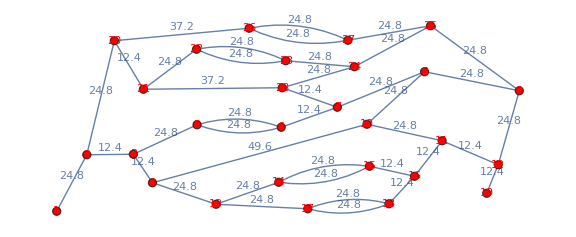

```mathematica
Graph[vl,edges,VertexCoordinates->{v_:>vd[[v, ;;2]]},EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",.5]},VertexSize->.3,VertexStyle->Red,ImageSize->Large]
```

```mathematica
GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}
```

GraphLayout→{SpringElectricalEmbedding,EdgeWeighted→True}

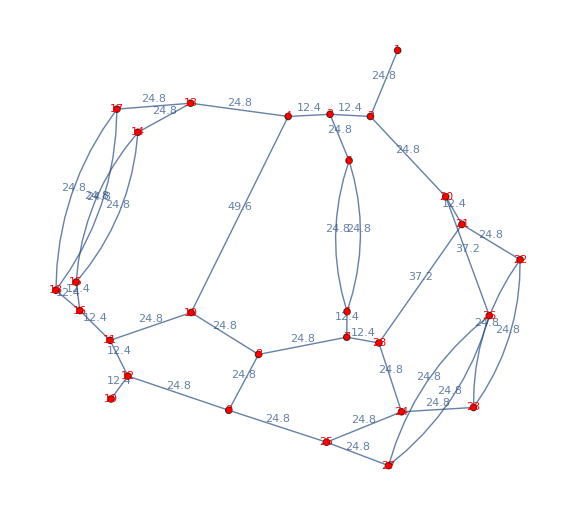

```mathematica
Graph[vl,edges,GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True},EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",.5]},VertexSize->.3,VertexStyle->Red,ImageSize->Large]
```

```mathematica
Graph3D[vl,edges,GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True},EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",.5]},VertexSize->.3,VertexStyle->Red,ImageSize->Large]
```

-Graphics3D-

```mathematica
vars=Array[Through[{x,y}@#]&,Length@vd]
```

{{x[1],y[1]},{x[2],y[2]},{x[3],y[3]},{x[4],y[4]},{x[5],y[5]},{x[6],y[6]},{x[7],y[7]},{x[8],y[8]},{x[9],y[9]},{x[10],y[10]},{x[11],y[11]},{x[12],y[12]},{x[13],y[13]},{x[14],y[14]},{x[15],y[15]},{x[16],y[16]},{x[17],y[17]},{x[18],y[18]},{x[19],y[19]},{x[20],y[20]},{x[21],y[21]},{x[22],y[22]},{x[23],y[23]},{x[24],y[24]},{x[25],y[25]},{x[26],y[26]},{x[27],y[27]},{x[28],y[28]}}

```mathematica
λ=1.;
obj=Total[(Norm[vars[[First@#]]-vars[[Last@#]]]-#/.ew)^2&/@EdgeList[g3d]]+λ Total[Norm/@(vars-vd[[All, ;;2]])];
```

```mathematica
solution=Last@Minimize[{obj,And@@Thread[0≤Join@@vars≤500]},Join@@vars];

edgeLengths=#->Norm[Through[{x,y}@First[#]]-Through[{x,y}@Last[#]]]/.solution&/@EdgeList[g3d];

Grid[Prepend[{#,#/.ew,#/.edgeLengths}&/@EdgeList[g3d],{"edge","EdgeWeight","Edge Length"}],Dividers->All]
```

edge | EdgeWeight | Edge Length
1<->2 | 24.8 | 24.2997
2<->3 | 12.4 | 12.3577
3<->4 | 12.4 | 12.147
3<->5 | 24.8 | 24.5392
5<->6 | 24.8 | 24.493
5<->6 | 24.8 | 24.493
6<->7 | 12.4 | 12.263
7<->8 | 24.8 | 24.8567
8<->9 | 24.8 | 24.5765
4<->10 | 49.6 | 48.9749
10<->11 | 24.8 | 24.255
10<->8 | 24.8 | 24.3412
11<->12 | 12.4 | 12.1247
4<->13 | 24.8 | 24.5765
13<->14 | 24.8 | 24.3443
14<->15 | 24.8 | 24.5748
14<->15 | 24.8 | 24.5748
15<->16 | 12.4 | 12.0875
13<->17 | 24.8 | 24.8775
17<->18 | 24.8 | 24.6088
17<->18 | 24.8 | 24.6088
18<->16 | 12.4 | 12.1695
16<->11 | 12.4 | 12.7331
12<->19 | 12.4 | 12.1968
2<->20 | 24.8 | 24.5989
20<->21 | 12.4 | 12.2712
21<->22 | 24.8 | 24.3878
22<->23 | 24.8 | 24.6043
22<->23 | 24.8 | 24.6043
23<->24 | 24.8 | 24.1378
24<->25 | 24.8 | 24.49
20<->26 | 37.2 | 36.9144
26<->27 | 24.8 | 24.4953
26<->27 | 24.8 | 24.4953
27<->25 | 24.8 | 24.611
25<->9 | 24.8 | 24.51
21<->28 | 37.2 | 37.1043
28<->7 | 12.4 | 12.0551
28<->24 | 24.8 | 24.8958
9<->12 | 24.8 | 24.7536

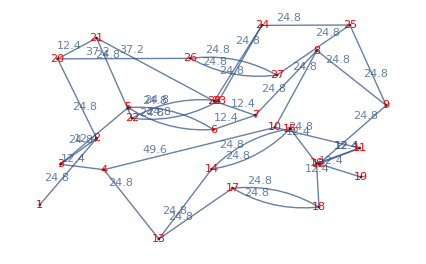

```mathematica
Graph[vl,edges,VertexCoordinates->{v_:>({x[v],y[v]}/.solution)},EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",.3]},VertexSize->.7,VertexStyle->Red]
```

```mathematica
vars3d=Array[Through[{x,y,z}@#]&,28];
```

```mathematica
λ=1/1.;

obj3d=Total[(Norm[vars3d[[First@#]]-vars3d[[Last@#]]]-#/.ew)^2&/@EdgeList[g3d]]+λ Total[Norm/@(vars3d-vd)];

solution3d=Last@Minimize[{obj3d,And@@Thread[0≤Join@@vars3d≤500]},Join@@vars3d];

edgeLengths3d=#->Norm[vars3d[[First@#]]-vars3d[[Last@#]]]/.solution3d&/@EdgeList[g3d];

Grid[Prepend[{#,#/.ew,#/.edgeLengths3d}&/@EdgeList[g3d],{"edge","EdgeWeight","Edge Length"}],Dividers->All]
```

edge | EdgeWeight | Edge Length
1<->2 | 24.8 | 24.3049
2<->3 | 12.4 | 12.4809
3<->4 | 12.4 | 12.0677
3<->5 | 24.8 | 24.5328
5<->6 | 24.8 | 24.609
5<->6 | 24.8 | 24.609
6<->7 | 12.4 | 12.2103
7<->8 | 24.8 | 24.7911
8<->9 | 24.8 | 24.5493
4<->10 | 49.6 | 49.4353
10<->11 | 24.8 | 24.8544
10<->8 | 24.8 | 24.4225
11<->12 | 12.4 | 12.7547
4<->13 | 24.8 | 24.7045
13<->14 | 24.8 | 24.4517
14<->15 | 24.8 | 24.5629
14<->15 | 24.8 | 24.5629
15<->16 | 12.4 | 11.6047
13<->17 | 24.8 | 24.6589
17<->18 | 24.8 | 24.6059
17<->18 | 24.8 | 24.6059
18<->16 | 12.4 | 12.1744
16<->11 | 12.4 | 12.1083
12<->19 | 12.4 | 11.8907
2<->20 | 24.8 | 24.6465
20<->21 | 12.4 | 12.561
21<->22 | 24.8 | 24.4838
22<->23 | 24.8 | 24.5644
22<->23 | 24.8 | 24.5644
23<->24 | 24.8 | 24.6239
24<->25 | 24.8 | 24.6145
20<->26 | 37.2 | 36.7276
26<->27 | 24.8 | 24.5103
26<->27 | 24.8 | 24.5103
27<->25 | 24.8 | 24.4827
25<->9 | 24.8 | 24.7341
21<->28 | 37.2 | 36.9961
28<->7 | 12.4 | 12.0595
28<->24 | 24.8 | 24.4564
9<->12 | 24.8 | 24.2889

```mathematica
Graph3D[vl,edges,VertexCoordinates->{v_:>({x[v],y[v],z[v]}/.solution3d)},EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",.5]},VertexSize->.3,VertexStyle->Red,ImageSize->Large]
```

-Graphics3D-

```mathematica
λby100=1/100.;

obj3d=Total[(Norm[vars3d[[First@#]]-vars3d[[Last@#]]]-#/.ew)^2&/@EdgeList[g3d]]+λby100 Total[Norm/@(vars3d-vd)];

solution3d=Last@Minimize[{obj3d,And@@Thread[0≤Join@@vars3d≤500]},Join@@vars3d];

edgeLengths3d=#->Norm[vars3d[[First@#]]-vars3d[[Last@#]]]/.solution3d&/@EdgeList[g3d];

Grid[Prepend[{#,#/.ew,#/.edgeLengths3d}&/@EdgeList[g3d],{"edge","EdgeWeight","Edge Length"}],Dividers->All]
```

edge | EdgeWeight | Edge Length
1<->2 | 24.8 | 24.7934
2<->3 | 12.4 | 12.3949
3<->4 | 12.4 | 12.3998
3<->5 | 24.8 | 24.7987
5<->6 | 24.8 | 24.7983
5<->6 | 24.8 | 24.7983
6<->7 | 12.4 | 12.3966
7<->8 | 24.8 | 24.7956
8<->9 | 24.8 | 24.7962
4<->10 | 49.6 | 49.5982
10<->11 | 24.8 | 24.796
10<->8 | 24.8 | 24.7965
11<->12 | 12.4 | 12.4001
4<->13 | 24.8 | 24.7972
13<->14 | 24.8 | 24.7976
14<->15 | 24.8 | 24.7971
14<->15 | 24.8 | 24.7971
15<->16 | 12.4 | 12.3932
13<->17 | 24.8 | 24.7972
17<->18 | 24.8 | 24.7979
17<->18 | 24.8 | 24.7979
18<->16 | 12.4 | 12.3969
16<->11 | 12.4 | 12.3971
12<->19 | 12.4 | 12.3945
2<->20 | 24.8 | 24.7922
20<->21 | 12.4 | 12.4037
21<->22 | 24.8 | 24.7893
22<->23 | 24.8 | 24.7987
22<->23 | 24.8 | 24.7987
23<->24 | 24.8 | 24.7962
24<->25 | 24.8 | 24.7992
20<->26 | 37.2 | 37.1953
26<->27 | 24.8 | 24.7958
26<->27 | 24.8 | 24.7958
27<->25 | 24.8 | 24.7964
25<->9 | 24.8 | 24.7986
21<->28 | 37.2 | 37.2061
28<->7 | 12.4 | 12.4034
28<->24 | 24.8 | 24.7999
9<->12 | 24.8 | 24.7981

```mathematica
Graph3D[vl,edges,VertexCoordinates->{v_:>({x[v],y[v],z[v]}/.solution3d)},EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",.5]},VertexSize->.3,VertexStyle->Red,ImageSize->Large]
```

-Graphics3D-

```mathematica
λby100=1/10.;

obj3d=Total[(Norm[vars3d[[First@#]]-vars3d[[Last@#]]]-#/.ew)^2&/@EdgeList[g3d]]+λby100 Total[Norm/@(vars3d-vd)];

solution3d=Last@Minimize[{obj3d,And@@Thread[0≤Join@@vars3d≤1000]},Join@@vars3d];

edgeLengths3d=#->Norm[vars3d[[First@#]]-vars3d[[Last@#]]]/.solution3d&/@EdgeList[g3d];

Grid[Prepend[{#,#/.ew,#/.edgeLengths3d}&/@EdgeList[g3d],{"edge","EdgeWeight","Edge Length"}],Dividers->All]
```

edge | EdgeWeight | Edge Length
1<->2 | 24.8 | 24.7494
2<->3 | 12.4 | 12.4025
3<->4 | 12.4 | 12.3843
3<->5 | 24.8 | 24.7645
5<->6 | 24.8 | 24.775
5<->6 | 24.8 | 24.775
6<->7 | 12.4 | 12.3804
7<->8 | 24.8 | 24.8407
8<->9 | 24.8 | 24.8107
4<->10 | 49.6 | 49.5491
10<->11 | 24.8 | 24.8042
10<->8 | 24.8 | 24.717
11<->12 | 12.4 | 12.3623
4<->13 | 24.8 | 24.7815
13<->14 | 24.8 | 24.7405
14<->15 | 24.8 | 24.7813
14<->15 | 24.8 | 24.7813
15<->16 | 12.4 | 12.3673
13<->17 | 24.8 | 24.8205
17<->18 | 24.8 | 24.7834
17<->18 | 24.8 | 24.7834
18<->16 | 12.4 | 12.3755
16<->11 | 12.4 | 12.3443
12<->19 | 12.4 | 12.3608
2<->20 | 24.8 | 24.7635
20<->21 | 12.4 | 12.4162
21<->22 | 24.8 | 24.7524
22<->23 | 24.8 | 24.7798
22<->23 | 24.8 | 24.7798
23<->24 | 24.8 | 24.7711
24<->25 | 24.8 | 24.779
20<->26 | 37.2 | 37.1604
26<->27 | 24.8 | 24.783
26<->27 | 24.8 | 24.783
27<->25 | 24.8 | 24.7585
25<->9 | 24.8 | 24.7667
21<->28 | 37.2 | 37.186
28<->7 | 12.4 | 12.4169
28<->24 | 24.8 | 24.7843
9<->12 | 24.8 | 24.7713

```mathematica
Graph3D[vl,edges,VertexCoordinates->{v_:>({x[v],y[v],z[v]}/.solution3d)},EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",.5]},VertexSize->.3,VertexStyle->Red,ImageSize->Large]
```

-Graphics3D-